# NG^21 P_08. Обучение с учителем. Дельта-правило обучения

Бельской Екатерины, 
2 курс, 5 группа

## 1. Трёхслойная нейронная сеть прямого распространения

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
ClearAll[LoadMNIST];
LoadMNIST[SetName_String]:=Module[{F,FDummy,Counter,Rows,Cols,Digits,Images},
F=OpenRead[ToLowerCase[SetName]<>"-images.idx3-ubyte",BinaryFormat->True];
{FDummy,Counter,Rows,Cols}=BinaryRead[F,Array["Integer32"&,4],ByteOrdering->+1];
Images=Fold[Partition[#,#2]&,BinaryReadList[F,"Byte",ByteOrdering->+1],{Cols,Rows}];
Close[F];
F=OpenRead[ToLowerCase[SetName]<>"-labels.idx1-ubyte",BinaryFormat->True];
{FDummy,Counter}=BinaryRead[F,Array["Integer32"&,2],ByteOrdering->+1];
Digits=BinaryReadList[F,"Byte",ByteOrdering->+1];
Close[F];
{Digits,Images}]
```

```mathematica
Map[Dimensions,Train=LoadMNIST["train"]]
```

{{60000},{60000,28,28}}

```mathematica
Map[Dimensions,Test=LoadMNIST["t10k"]]
```

{{10000},{10000,28,28}}

### 1.1 Стандартизация входных данных

Первый слой нейронов

```mathematica
kmLayer1[rastr_]:=Append[(rastr/255.)//Flatten,1];
```

```mathematica
Timing[km$X=kmLayer1[#]&/@Train⟦2⟧;]
```

{1.29688,Null}

Наборов из векторов, где каждой нарисованной цифре соответствует список из 10 ти 0 и одной 1 цы, занимающей соответствующую позицию

```mathematica
km$Y=UnitVector[10,#+1]&/@Train⟦1⟧;
```

```mathematica
a=kmLayer1[Train⟦2,1⟧];
```

```mathematica
Dimensions[Train⟦2,1⟧]
```

{28,28}

```mathematica
a//Length
```

785

### 1.2 Слой нейронов

Матрица весов всех нейронов данного слоя

```mathematica
kmWeight=RandomReal[{-1,1},{10,785}];
```

```mathematica
kmWeight.a
```

{-1.11729,-9.51273,-4.27522,7.08372,6.90814,-14.563,10.0274,2.65711,1.41432,-5.89051}

Второй слой неронов

```mathematica
ClearAll[kmLayer2]
```

```mathematica
kmLayer2[vect_]:=kmWeight.vect;
```

```mathematica
kmLayer2[a]
```

{-1.11729,-9.51273,-4.27522,7.08372,6.90814,-14.563,10.0274,2.65711,1.41432,-5.89051}

### 1.3 Функция активации

Она же третий слой нейронов

```mathematica
ClearAll[softMax];
softMax[X_]:=With[{exp=Exp[X]},exp/Total[exp]];
```

```mathematica
softMax[kmWeight.a]
```

{0.0000131653,2.97399×10^-9,5.59711×10^-7,0.0479828,0.0402564,1.90563×10^-11,0.911008,0.000573633,0.000165539,1.11289×10^-7}

### 1.4 Сеть прямого распространения

```mathematica
ClearAll[kmANN];
kmANN=RightComposition[kmLayer2,softMax];
```

```mathematica
kmANN[km$X⟦1⟧]
```

{0.0000131653,2.97399×10^-9,5.59711×10^-7,0.0479828,0.0402564,1.90563×10^-11,0.911008,0.000573633,0.000165539,1.11289×10^-7}

## 2. Потери : перекрёстная энтропия, дельта правило

Функция потерь

```mathematica
ClearAll[kmLoss];
kmLoss[Y_,YT_]:=-YT.RealExponent[Y,ⅇ];
```

```mathematica
Log[0.]
```

Indeterminate

```mathematica
RealExponent[0.,ⅇ]
```

-745.133

```mathematica
kmLoss[kmLayer2[km$X⟦1⟧],km$Y⟦1⟧]
```

-1.40695

```mathematica
Total[MapThread[kmLoss[kmLayer2[#1],#2]&,{km$X,km$Y}]]/60000
```

-0.957379

## 3. Дельта правило обучения

Процедура обучения нейрона. Вычисляет значение функции потерь и поправку весовых коэффициентов для минипакета

```mathematica
ClearAll[kmTrain];
kmTrain[{X_,YT_}]:=({kmANN[X]-YT}ᵀ).{X};
kmTrain[Xlist_,YTlist_]:=MapThread[-kmTrain[{#1,#2}]&, {Xlist, YTlist}];
```

```mathematica
Dimensions@kmTrain[{km$X⟦1⟧, km$Y⟦1⟧}]
```

{10,785}

```mathematica
Dimensions@Mean[kmTrain[km$X⟦1;;20⟧,km$Y⟦1;;20⟧]]
```

{10,785}

## 4. Подбор оптимальных параметров обучения

```mathematica
Timing[km$X=kmLayer1[#]&/@Train⟦2⟧;]
```

{0.90625,Null}

```mathematica
km$Y=UnitVector[10,#+1]&/@Train⟦1⟧;
```

Итоговая процедура обучения нейрона

```mathematica
kmTrain[miniBatch_,η0_Real,Steps_Integer,W0_List]:=(η=η0;
Stepss=Steps;
loss=0;
li={};
len=(60000/miniBatch);
ep=Ceiling[Steps/len];
While[ep≠0,
l=Partition[RandomSample[Range[60000],60000],miniBatch];
If[Stepss-len<0,st=Stepss,st=len];
Do[
kmWeight=Total@(η*kmTrain[km$X⟦l⟦i⟧⟧,km$Y⟦l⟦i⟧⟧])+kmWeight;
loss=Total[MapThread[kmLoss[kmANN[#1],#2]&,{km$X⟦l⟦i⟧⟧,km$Y⟦l⟦i⟧⟧}]]/miniBatch;
AppendTo[li,loss],{i,st}];
Stepss=Stepss-len;
η=0.5*η;ep--])
```

```mathematica
kmWeight=ConstantArray[0,{10,785}];
```

```mathematica
Timing@kmTrain[10,0.1,4000,kmWeight]
```

{4.09375,Null}

```mathematica
Dimensions@kmWeight
```

{10,785}

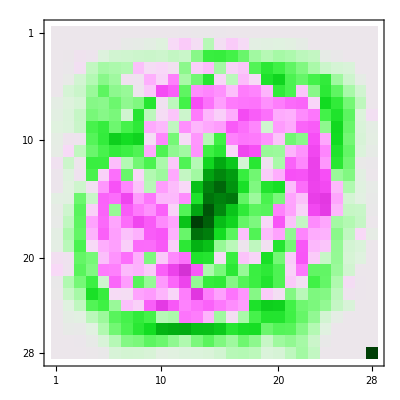
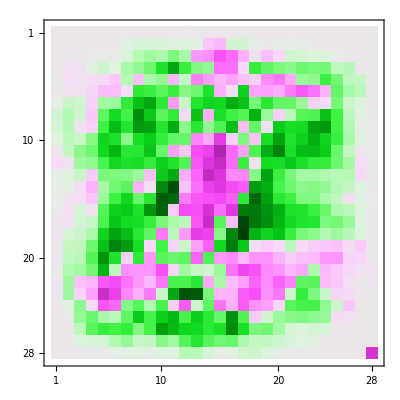
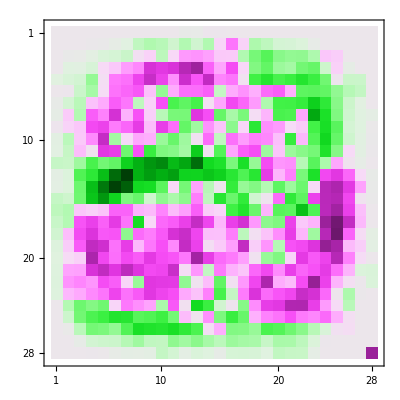
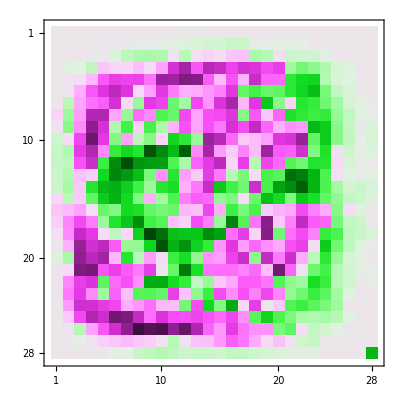
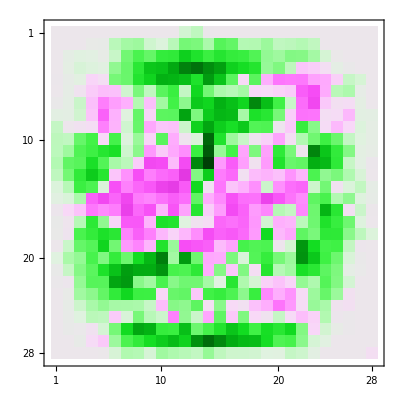
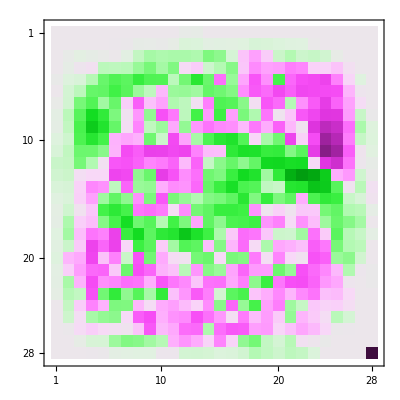
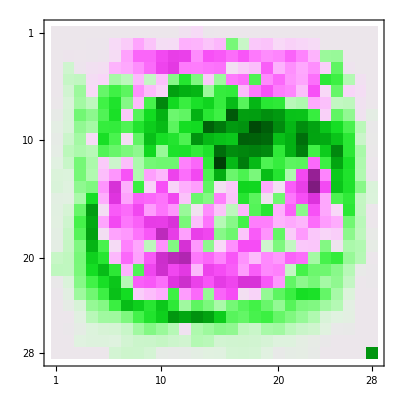
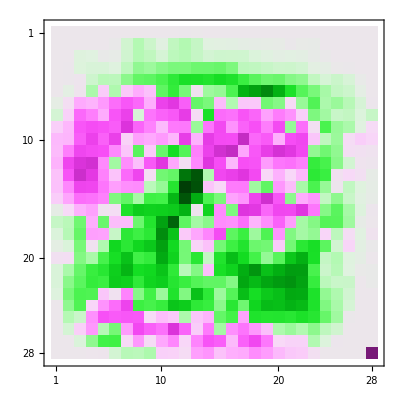

```mathematica
(MatrixPlot[Partition[Drop[kmWeight⟦#⟧,1],28],ColorFunction->"GreenPinkTones"])&/@Range[Length@kmWeight]
```

```mathematica
kmWeight
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.16214×10^-15,-4.66893×10^-14,-4.66878×10^-14,-1.94533×10^-15,0.,0.,0.,0.,0.,0.,0.,739,-0.000173234,-0.000984478,-0.000895786,-0.00016909,-1.51073×10^-7,-1.57817×10^-6,-0.0000171083,-0.0000232416,-0.0000826084,-0.0016683,-0.0726726,-0.0799653,-0.048801,-0.0000629588,-0.000220778,-0.0423976,-0.144079,-0.0333735,0.,0.,0.,0.,-3.55292},8,{1}}
 |  |  |  |

## 5. Качество распознавания

```mathematica
ClearAll[km$X,km$Y];
```

```mathematica
Timing[km$X=kmLayer1[#]&/@Test⟦2⟧;]
```

{0.140625,Null}

```mathematica
kmANN@km$X⟦1⟧
```

{8.82297×10^-21,1.86659×10^-32,1.71191×10^-12,5.44337×10^-9,1.5091×10^-18,4.42688×10^-15,3.03928×10^-33,1.,2.76146×10^-17,5.86808×10^-12}

```mathematica
km$Y=UnitVector[10,#+1]&/@Test⟦1⟧;
```

```mathematica
wrong={};
```

```mathematica
testRes=kmANN[km$X⟦#⟧]&/@Range[10000];
```

```mathematica
Position[kmANN@km$X⟦3⟧,Max[kmANN@km$X⟦3⟧]]==Position[km$Y⟦3⟧,1]
```

True

```mathematica
Do[If[Position[testRes⟦i⟧,Max[testRes⟦i⟧]]!=Position[km$Y⟦i⟧,1],AppendTo[wrong,i]],{i,10000}]
```

```mathematica
wrong//Length
```

1179

Процент неправильно распознанных растров

```mathematica
N[%/10000]*100
```

11.79

Среднее значение функции потерь

```mathematica
Total[kmLoss[testRes⟦#⟧,km$Y⟦#⟧]&/@wrong]/Length[wrong]
```

7.48844

Таблица некторых неправильно распознанных растров

```mathematica
ClearAll[kmDigits];
kmDigits[ind_,intRow_]:=Grid[Partition[Tooltip[ArrayPlot[Test⟦2,ind⟦#⟧⟧],First@First@Position[testRes⟦#⟧,Max[testRes⟦#⟧]]-1]&/@Range[Length@ind],intRow],Spacings->{0, 0},ItemSize->3]
```

```mathematica
kmDigits[wrong⟦1;;40⟧,10]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-